```mathematica
σ[En_,a_]:=(√(1-En^2))/a;
γ[En_,V0_,a_]:=(√(1-(En+V0)^2))/a;
λ[En_,V0_,a_]:=(√(a^2-4 V0^2))/(2 a);
```

### Plot 1

```mathematica
L=2;
a=10;
eq16[En_?NumericQ,V0_?NumericQ]:=Module[{s,g,l,y0,num1,den1,num2,den2,term1,term2},s=σ[En,a];
g=γ[En,V0,a];
l=λ[En,V0,a];
y0=(1+Exp[-a L])^-1;
(*first fraction*)num1=Hypergeometric2F1[3/2+g+s-l,3/2+g+s+l,2+2 s,y0];
den1=Hypergeometric2F1[1/2+g+s-l,1/2+g+s+l,1+2 s,y0];
term1=(1/2+g+s-l) (1/2+g+s+l) num1/den1;
(*second fraction*)num2=Hypergeometric2F1[3/2-g+s-l,3/2-g+s+l,2+2 s,y0];
den2=Hypergeometric2F1[1/2-g+s-l,1/2-g+s+l,1+2 s,y0];
term2=(1/2-g+s-l) (1/2-g+s+l) num2/den2;
(*whole left–hand side of (16)*)(term1+term2)/(1+2 s)+2 s (1+Exp[-a L])];
```

```mathematica
eq[En_,V0_]:=eq16[En,V0];

vList=Range[0.0,2.09,0.01];

roots=Reap[Module[{sol,Eguess=0.95},Do[sol=Quiet@FindRoot[eq[En,v]==0,{En,Eguess},WorkingPrecision->30,MaxIterations->80];
Eguess=En/. sol;(*use previous root as guess*)Sow[{v,Eguess}],{v,vList}]]][[2,1]];
```

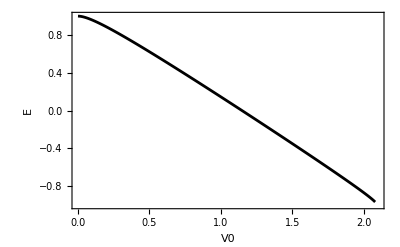

```mathematica
ListLinePlot[roots,FrameLabel->{"V0","E"},PlotRange->{{0,2.1},{-1,1}},Frame->True,PlotStyle->Black]
```

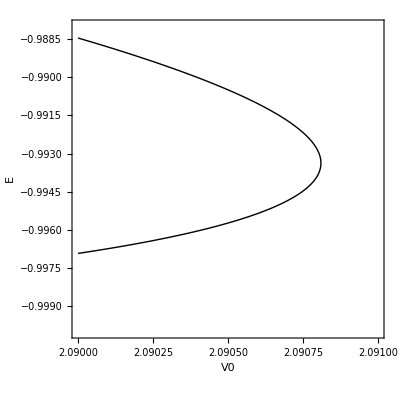

```mathematica
ContourPlot[eq16[En,V0],{V0,2.09,2.091},{En,-1,-0.988},Contours->{0},ContourStyle->{Thick,Black},ContourShading->None,FrameLabel->{"V0","E"},PlotPoints->60,MaxRecursion->4]
```

### Plot 2

```mathematica
Clear[L,a]
```

```mathematica
L=2;
a=2;
eq16[En_?NumericQ,V0_?NumericQ]:=Module[{s,g,l,y0,num1,den1,num2,den2,term1,term2},s=σ[En,a];
g=γ[En,V0,a];
l=λ[En,V0,a];
y0=(1+Exp[-a L])^-1;
(*first fraction*)num1=Hypergeometric2F1[3/2+g+s-l,3/2+g+s+l,2+2 s,y0];
den1=Hypergeometric2F1[1/2+g+s-l,1/2+g+s+l,1+2 s,y0];
term1=(1/2+g+s-l) (1/2+g+s+l) num1/den1;
(*second fraction*)num2=Hypergeometric2F1[3/2-g+s-l,3/2-g+s+l,2+2 s,y0];
den2=Hypergeometric2F1[1/2-g+s-l,1/2-g+s+l,1+2 s,y0];
term2=(1/2-g+s-l) (1/2-g+s+l) num2/den2;
(*whole left–hand side of (16)*)(term1+term2)/(1+2 s)+2 s (1+Exp[-a L])];
```

```mathematica
eq[En_,V0_]:=eq16[En,V0];

vList=Range[0.0,2.35,0.01];

roots=Reap[Module[{sol,Eguess=0.95},Do[sol=Quiet@FindRoot[eq[En,v]==0,{En,Eguess},WorkingPrecision->30,MaxIterations->80];
Eguess=En/. sol;(*use previous root as guess*)Sow[{v,Eguess}],{v,vList}]]][[2,1]];
```

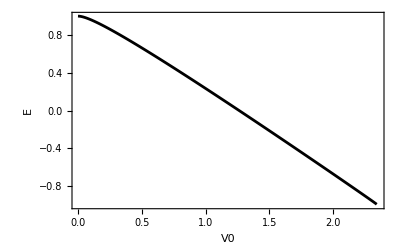

```mathematica
ListLinePlot[roots,FrameLabel->{"V0","E"},PlotRange->{{0,2.35},{-1,1}},Frame->True,PlotStyle->Black]
```

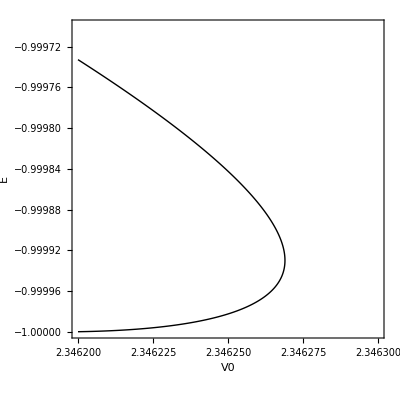

```mathematica
ContourPlot[eq16[En,V0],{V0,2.3462,2.3463},{En,-1,-0.99970},Contours->{0},ContourStyle->{Thick,Black},ContourShading->None,FrameLabel->{"V0","E"},PlotPoints->60,MaxRecursion->4]
```